```mathematica
makeCluster[center_,stdDev_:0.5]:=
Thread[Table[RandomVariate[Apply[NormalDistribution, {x,stdDev}],100],{x,center}]];
```

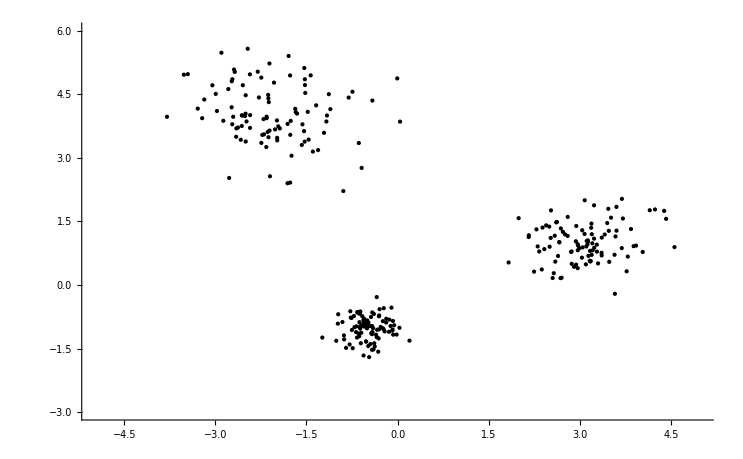

```mathematica
Show[ListPlot[makeCluster[{3,1},0.5],PlotStyle->Directive[Black,PointSize[Large]]],ListPlot[makeCluster[{-2,4},0.75],PlotStyle->Directive[Black,PointSize[Large]]], ListPlot[makeCluster[{-0.5,-1},0.25], PlotStyle->Directive[Black,PointSize[Large]]], PlotRange->{{-5,5},{-3,6}}, Axes->True]
```

```mathematica
(* The workhorse functions for k-means clustering *)
closest[x_, means_]:=means⟦First[Ordering[Map[EuclideanDistance[x,#]&,means]]]⟧;
partition[points_, means_]:=GatherBy[points, closest[#,means]&];
updatePartition[points_,old_]:=partition[points,Map[Mean,old]];
```

```mathematica
(* The entire k-means algorithm *)
kMeans[points_, initialMeans_]:= FixedPoint[updatePartition[points,#]&, partition[points, initialMeans]];
```

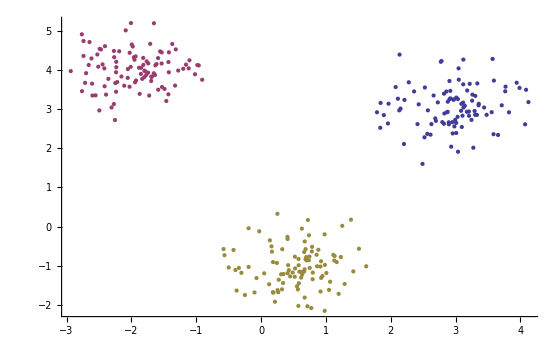

```mathematica
(* example usage *)
pts = Flatten[Table[makeCluster[x,0.5],{x,{{3,3}, {-2,4}, {0.5,-1}}}],1];
(*pts = {{0,1},{3,3},{-5,-1},{3.1,2.8}};*)
initialMeans = RandomSample[pts,3];
clustering = kMeans[pts, initialMeans];

(* plotting *)
ListPlot[clustering,PlotStyle->PointSize[Large]]
```

```mathematica
kMeansAnimate[points_, initialMeans_]:=FixedPointList[updatePartition[points,#]&, partition[points, initialMeans]];
```

```mathematica
pts = Flatten[Table[makeCluster[x,0.5],{x,{{0.5,0.5}, {-0.5,0.5}, {0.5,-0.5}}}],1];
clusteringSequence = kMeansAnimate[pts, RandomSample[pts,3]];
```

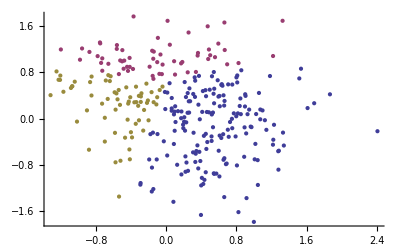
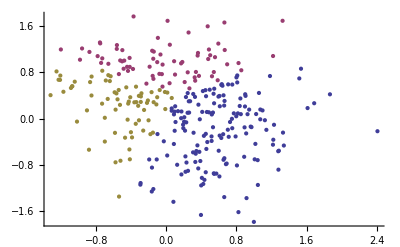
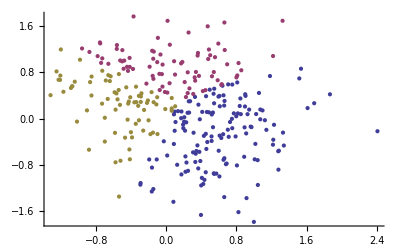
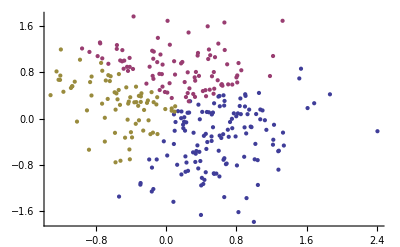
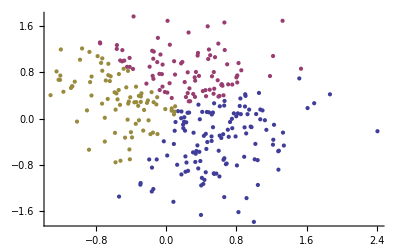
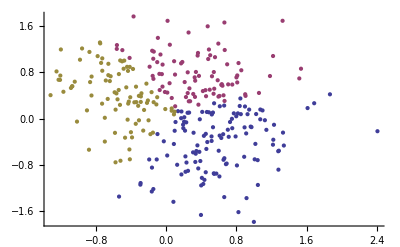
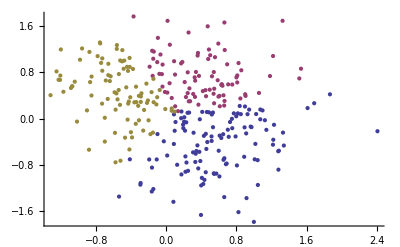
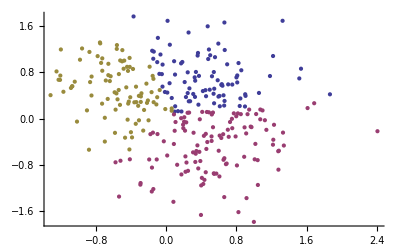
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
frames=Map[ListPlot[#,PlotStyle->PointSize[Large]]&,clusteringSequence]
```

```mathematica
(* Export["k-means-animation.gif",frames,"DisplayDurations"->0.25]; *)
```

```mathematica
L={{39.3,14.59},{12.38,6.25},{24.4,4.3},{22.9,4.6},{9.26,6.52},{39.36,12.06},{12.9,4.41},{16.19,5.72},{17.34,7.36},{12.9,8.49},{12.76,7.92},{12.28,6.94},{8.69,10.23},{17.3,7.13},{15.95,6.91},{14.41,2.63},{22.53,5.71},{12.23,8.39},{11.1,13.9},{10.03,10.63},{26.02,5.91},{37.55,8.79},{11.42,7.74},{18.75,6.99},{24.24,6.76},{8.9,9.4},{22.02,12.0},{15.2,6.5},{10.69,4.82},{17.74,3.39},{9.2,14.32},{43.2,12.47},{19.11,8.1},{40.58,9.36},{25.17,7.97},{32.49,11.66},{10.28,8.09},{21.21,6.28},{12.21,5.19},{36.13,14.71},{38.7,15.16},{14.3,5.8},{12.31,7.17},{17.23,5.29},{31.49,8.19},{37.05,10.8},{40.09,11.25},{15.22,7.61},{16.4,4.38},{30.4,9.96},{9.57,11.99},{9.96,7.52},{11.44,6.48},{8.62,10.94},{10.22,10.19},{24.91,8.08},{15.6,8.03},{19.44,4.41},{19.6,5.01},{24.22,4.8},{17.44,5.63},{34.88,8.81},{32.1,7.92},{10.43,13.6},{38.5,9.3},{13.14,8.67},{20.7,5.93},{10.36,10.33},{12.7,8.9},{15.92,4.76},{35.0,13.07},{33.41,7.5},{34.3,3.22},{10.75,10.05},{8.33,11.04},{32.0,7.7},{14.22,8.27},{9.08,10.8},{14.58,8.22},{16.81,7.98},{17.5,4.9},{26.48,4.92},{10.04,8.52},{36.6,10.19},{34.72,15.01},{16.69,7.18},{23.87,8.1},{24.66,5.05},{7.54,7.23},{9.49,12.7},{13.23,7.02},{20.6,7.43},{17.7,6.3},{18.52,5.94},{28.19,4.73},{15.81,6.38},{11.36,9.95},{18.97,5.5},{9.06,9.93},{18.89,6.59},{8.39,9.15},{11.12,7.56},{26.52,2.74},{20.44,8.52},{31.93,7.26},{22.45,7.31},{14.51,9.12},{8.42,6.38},{20.96,2.13},{23.9,6.9},{25.68,7.99},{9.97,13.6},{14.92,6.63},{26.65,15.18},{36.45,10.36},{17.5,4.9},{10.76,6.78},{9.34,11.4},{11.7,8.5},{9.05,3.85},{11.8,8.95},{34.0,7.3},{40.42,12.84},{20.74,4.95},{15.12,3.76},{46.6,13.9},{10.31,8.72},{28.14,4.31},{32.78,8.66},{13.78,6.73},{18.87,4.9},{21.85,4.31},{12.5,12.62},{6.85,8.52},{20.7,6.01},{10.89,9.03},{11.62,6.78},{18.97,4.76},{39.34,12.79},{21.11,13.09},{27.08,5.97},{21.85,6.75},{10.89,8.39},{16.05,5.34},{13.57,7.2},{19.12,5.04},{47.6,13.4},{39.23,13.48},{20.2,3.4},{10.8,9.22},{24.33,3.42},{24.3,6.8},{10.79,7.89},{19.17,4.69},{25.92,6.56},{17.22,4.59},{19.13,5.95},{24.98,4.98},{9.96,10.24},{9.76,10.86},{11.3,8.0},{10.23,1.55},{9.49,11.84},{12.3,14.1},{36.14,9.64},{10.48,6.99},{13.9,7.08},{14.42,7.1},{8.06,8.92},{14.36,7.02},{22.1,5.34},{8.9,8.06},{37.02,7.93},{19.19,3.32},{36.19,9.05},{9.17,13.81},{15.1,6.9},{38.12,11.49},{7.72,3.41},{10.38,9.64},{8.76,11.0},{27.46,3.91},{42.12,14.55},{19.32,17.23},{10.4,8.88},{17.04,5.96},{31.7,8.3},{17.44,6.17},{26.16,14.21},{10.24,10.21},{10.4,8.1},{23.52,3.67},{8.7,6.7},{25.93,6.49},{37.7,8.6},{12.81,7.38},{35.2,6.4},{35.26,7.78},{24.7,4.88},{14.25,8.35},{17.28,5.87},{17.58,6.1},{19.55,6.21},{17.44,3.0},{23.35,9.13},{45.8,11.6},{9.59,15.76},{15.76,2.04},{12.27,9.33},{13.7,8.4},{13.4,9.55},{17.33,5.29},{27.0,4.3},{19.88,5.2},{16.83,5.95},{10.9,7.7},{13.91,4.79},{24.19,3.56},{31.65,8.8},{32.57,6.82},{43.1,13.4},{32.19,12.38}};
```

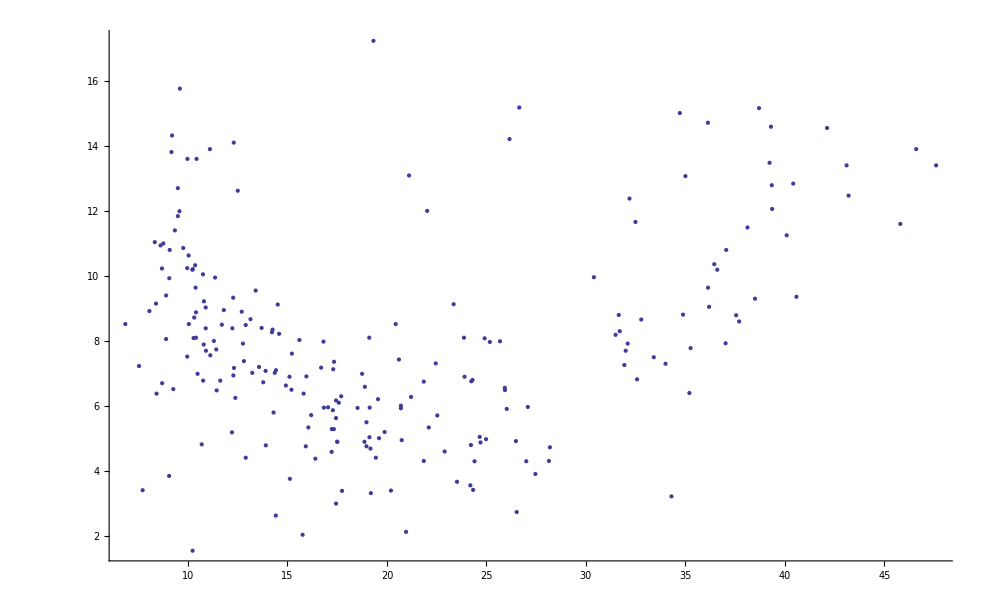

```mathematica
ListPlot[L,PlotStyle->PointSize[Large]]
```

```mathematica
plotCountriesKMeans[k_]:=Module[{M,countriesClusters},
M = Transpose[Map[Standardize,Transpose[L]]];
countriesClusters=kMeans[M, RandomSample[M,k]];
ListPlot[countriesClusters,PlotStyle->PointSize[.03]]
];
```

```mathematica
Table[plotCountriesKMeans[k],{k,2,7}] // TableForm
```